# My glucose series

## Program

```mathematica
getTimeSer[gs_]:=Module[{tr},
tr=Transpose[gs];
TimeSeries[tr[[2]],{tr[[1]]}]]
```

## Data

```mathematica
gs=Get["/Users/kouamano/Profile/blood-glc.txt"]
```

{{Thu 3 Feb 2022 06:05:00GMT+9,148,{}},{Thu 3 Feb 2022 11:16:00GMT+9,396,{}},{Thu 3 Feb 2022 16:31:00GMT+9,257,{}},{Fri 4 Feb 2022 06:06:00GMT+9,177,{}},{Fri 4 Feb 2022 11:16:00GMT+9,273,{}},{Fri 4 Feb 2022 18:30:00GMT+9,204,{}},{Sat 5 Feb 2022 05:57:00GMT+9,98,{}},{Sat 5 Feb 2022 12:15:00GMT+9,137,{}},{Sat 5 Feb 2022 17:15:00GMT+9,226,{}},{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Sun 6 Feb 2022 12:21:00GMT+9,374,{}},{Sun 6 Feb 2022 17:28:00GMT+9,241,{}},{Mon 7 Feb 2022 06:17:00GMT+9,158,{}},{Mon 7 Feb 2022 11:34:00GMT+9,293,{}},{Mon 7 Feb 2022 16:44:00GMT+9,382,{}},{Tue 8 Feb 2022 06:23:00GMT+9,152,{}},{Tue 8 Feb 2022 12:09:00GMT+9,399,{}},{Tue 8 Feb 2022 17:05:00GMT+9,275,{}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}}}

```mathematica
gts=getTimeSer[gs]
```

TimeSeries[…]

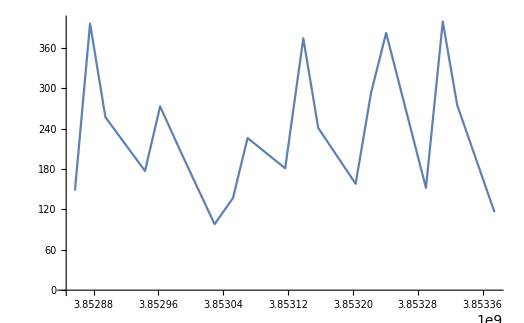

```mathematica
ListLinePlot[gts]
```